```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="BrickRed";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

```mathematica
theoList={{0.5,0.0403},{1.67, 0.074},{2.0,0.0973},{3,0.1318},{4,0.227592},{5,0.24502},{6,0.2687},{8,0.36},{13,0.624},{15,0.78},{16.7, 0.8714},{18,0.904}}
```

{{0.5,0.0403},{1.67,0.074},{2.,0.0973},{3,0.1318},{4,0.227592},{5,0.24502},{6,0.2687},{8,0.36},{13,0.624},{15,0.78},{16.7,0.8714},{18,0.904}}

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11,559/1000},{12,602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000}}
```

{{0.5,23/1000},{1.67,39/500},{2,19/200},{6,36/125},{8,391/1000},{10,469/1000},{11,559/1000},{12,301/500},{13,637/1000},{14,357/500},{15,387/500},{16,839/1000},{16.7,893/1000},{17,114/125}}

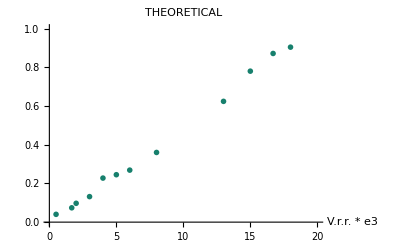

```mathematica
PlotTheoretical=ListPlot[theoList, 
PlotStyle->{ColorData["Crayola"][theoreticalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"THEORETICAL"]
```

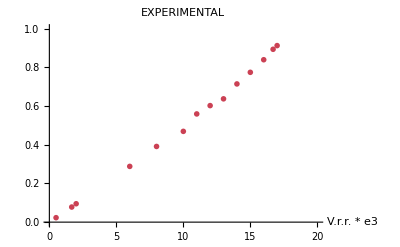

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"EXPERIMENTAL"]
```

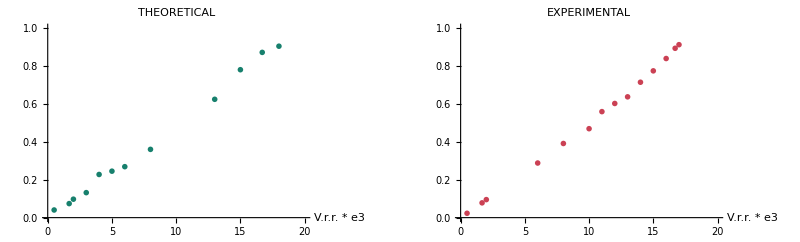

```mathematica
GraphicsRow[{PlotTheoretical, PlotExperimental}]
```

```mathematica
Rasterize[ListPlot[{theoList,experimentalList},
PlotLegends->{"theoretical","experimental"},PlotStyle->{{ColorData["Crayola"][theoreticalColor],Thickness[0.01]}, {ColorData["Crayola"][experimentalColor],Thickness[0.01]}},
PlotLabel->Style["Probability of extinction",20,FontOpacity->0.999],
Frame->True,
FrameLabel->{Style["Virus removal rate * E3",15,FontOpacity->0.999],""},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->15]]]
```

-Graphics-

## Geometric distribution

The relative frequency of 0.

```mathematica
theoFreqZeroList={{0.5,19/1000},{2.0,89/1000},{3,114/1000},{4,191/1000},{5,189/1000},{6,212/1000},{8,270/1000},{13,376/1000},{15,421/1000},{16.7, 460/1000},{18,466/1000}}
```

{{0.5,19/1000},{2.,89/1000},{3,57/500},{4,191/1000},{5,189/1000},{6,53/250},{8,27/100},{13,47/125},{15,421/1000},{16.7,23/50},{18,233/500}}

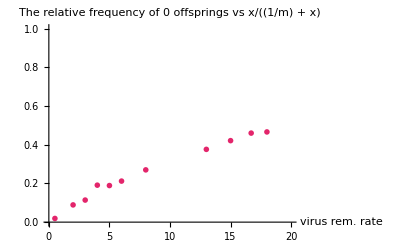

```mathematica
PlotZeroFreq=ListPlot[theoFreqZeroList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"virus rem. rate",""},PlotLabel->"The relative frequency of 0 offsprings vs x/((1/m) + x)"]
```

```mathematica
F[p_]:=(1-Sqrt[1-4*(1-(p))*(p)])/(2*(1-(p)))
```

```mathematica
theoFreqZeroListAtF={{0.5,F[19/1000]},{2.0,F[89/1000]},{3,F[114/1000]},{4,F[191/1000]},{5,F[189/1000]},{6,F[212/1000]},{8,F[270/1000]},{13,F[376/1000]},{15,F[421/1000]},{16.7, F[460/1000]},{18,F[466/1000]}};
```

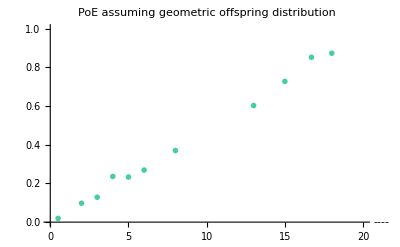

```mathematica
PlotZeroFreqAtF=ListPlot[theoFreqZeroListAtF, 
PlotStyle->{ColorData["Crayola"][zeroFreqColorAtF],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"----",""},PlotLabel->"PoE assuming geometric offspring distribution"]
```

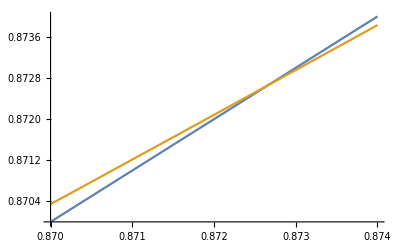

```mathematica
Plot[{x,(466/1000)/(1-(1-(466/1000))*x)},{x,0.87,0.874}]
```

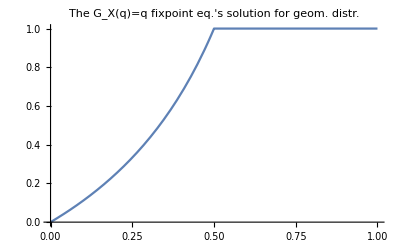

```mathematica
Plot[N[(1-Sqrt[1-4*(1-(p))*(p)])/(2*(1-(p)))],{p,0,1},PlotLabel->"The G_X(q)=q fixpoint eq.'s solution for geom. distr."]
```

```mathematica
Solve[(1-Sqrt[1-4*(1-(y))*(y)])/(2*(1-(y)))==(1/20)*x,y]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{y→x/(20+x)}}

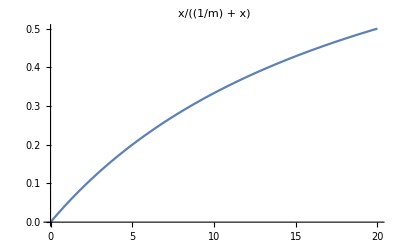

```mathematica
curvePlot=Plot[x/(20+x),{x,0,20},PlotLabel->"x/((1/m) + x)"]
```

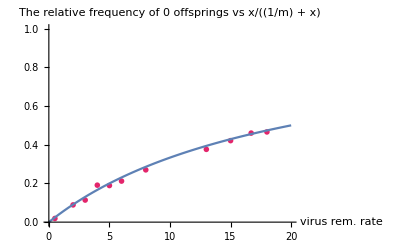

```mathematica
Show[PlotZeroFreq,curvePlot]
```